# Лабораторная работа 2.

Шпак Андрей, 3 курс, 5 группа.

## Задание 1. Гармонические колебания.

m - масса физического тела, r(t) - координата тела вдоль оси пружины. r = 0 положение равновесия, r(t) > 0, когда пружина растянута. r(t) < 0, когда она сжата. L - расстояние между положением равновесия и стенкой.

```mathematica
(*Фото*)
```

```mathematica
ClearAll[r0,v0,L,ω];
```

```mathematica
sol=DSolveValue[{r''[t]+ω^2*r[t]==0,r[0]==r0,r'[0]==v0},r[t],t]
```

(r0 ω Cos[t ω]+v0 Sin[t ω])/ω

```mathematica
pointMovesEqu[r0_,v0_,ω_,t_]:=(r0*ω*Cos[t*ω]+v0*Sin[t*ω])/ω
```

```mathematica
Manipulate[Animate[Graphics[{Red,Line[{{0,0},{L+Sqrt[r0^2+v0^2/ω^2]*Cos[ω*t+ArcTan[-v0/(ω*r0)]],0}}],Black,PointSize@0.03,Point[{L+Sqrt[r0^2+v0^2/ω^2]*Cos[ω*t+ArcTan[-v0/(ω*r0)]],0}],Line[{{0,-100},{0,100}}]},PlotRange->{{-10,10},{-10,10}}],{t,0,10},AnimationRunning->(L+Sqrt[r0^2+v0^2/ω^2]*Cos[ω*t+ArcTan[-v0/(ω*r0)]]>0)],{r0,1,10},{v0,0,10},{ω,1,10},{L,1,10}]
```

## Задание 2. Колебания с учетом сопротивления среды.

```mathematica
ClearAll[r0,v0,L,ω];
```

```mathematica
DSolveValue[{m*r''[t]==-k*r[t]-μ*r'[t],r[0]==r0,r'[0]==v0},r[t],t]
```

ⅇ^-t (r0+r0 t+t v0)

Нужно ввести замену, как в механике, что и очевидно: v= dr/dt. Тогда уравнения примет вид m*v’[t] == -k*r[t] - μ*v. Нужно разделить на m обе части.

```mathematica
(*Фото*)
```

Для получения каких-либо результатов, мы будем сравнивать μ и значение 4k*m, вывод которого я получил из записей выше. Но, так как константа 4m у нас постоянная величина, то фактически сравнение идет между μ и k. 
	Затухающие колебания - коэффициент вязкого трения меньше значения 4k*m. Устойчивый фокус.

```mathematica
k=1;
m=1;
μ=1;
```

```mathematica
μ^2-4k*m
```

-3

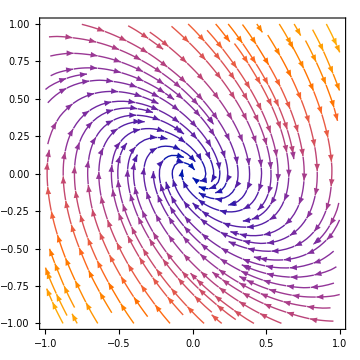

```mathematica
StreamPlot[{v,-k/m*r-μ/m*v},{r,-1,1},{v,-1,1}]
```

Критические колебания, коэффициент вязкого трения равен значению 4 k*m. Это будет устойчивый узел.

```mathematica
μ=Sqrt[4k*m];
```

```mathematica
μ^2-4k*m
```

0

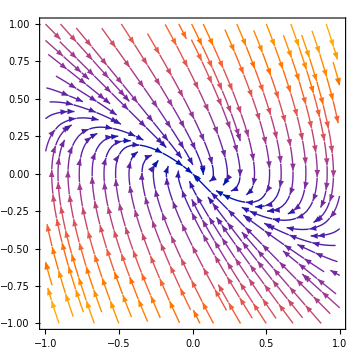

```mathematica
StreamPlot[{v,-k/m*r-μ/m*v},{r,-1,1},{v,-1,1}]
```

Апериодическое затухание. Коэффициент вязкого трения больше, чем значение 4 k*m - устойчивый узел.

```mathematica
μ=5;
```

```mathematica
μ^2-4k*m
```

21

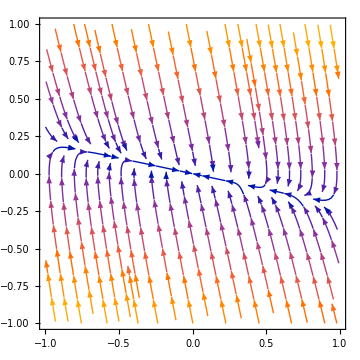

```mathematica
StreamPlot[{v,-k/m*r-μ/m*v},{r,-1,1},{v,-1,1}]
```

Выводы согласуются с аналитическим решением на листике.

Частные случаи. Сравним μ^2 и 4 ω^2 m:

```mathematica
k=0.001;
m=1;
μ=1.82*10^-5;
```

```mathematica
μ^2-4k*m
```

-3.9375

```mathematica
μ=1.002*10^-3;
```

```mathematica
μ^2-4k*m
```

-4.

```mathematica
μ=1.49;
```

```mathematica
μ^2-4k*m
```

-1.7799

Везде получены отрицательные значения и значит решения характерестического уравнения будут комплексными с отрицательной действительной частью, что свидетельствует о затухающий колебаниях.

## Задание 3. Вынужденные колебания.

## Задание 4. Система химических реакций двух веществ.

X - вещество, которое поступает в систему с постоянной скоростью k_1=const>0, превращается в вещество Y со скоростью, пропорциональной концентрации вещества X и коэффициентом пропорциональности k_2=const>0. Вещество Y выводится из системы со скоростью, пропорциональной концентрации вещества Y, и коэффициентом пропорциональности k_3=const>0. x(0) = x_0, y(0)=y_0,

```mathematica
X'[t]=Subscript[k, 1]-Subscript[k, 2]*X[t]
Y'[t]=Subscript[k, 3]*Y[t]
```

К УСР:
Основные понятия: первая лекция, определения, модель, моделирование, классификация моделирования, одномерные системы, постановки задачи, мат модель. Точка покоя, состояние равновесия, понятие устойчивости по решению, по Ляпунову, фазовые портреты, примеры. Вид задачи, концептуальная задача, после которой мы строим концептуальную модель. Отличие постановок задач. Колебания, популяции, системы второго порядка, примеры, хищник-жертва, химическая реакция. Типы положений равновесия, узел, седло, фокус, стенка. Фазовые портреты, состояния равновесия по характеристическим значениям, устойчивость по Ляпунову.